(ẋ)_1=1/(m1+m2+mb)(2 g (2 m1+m2-mb) t μ+A0 ω (2 m2 Cos[γ]+(m1+m2+mb) Cos[t ω]-(m1-m2+mb) Cos[γ+t ω]))
x_1=(g (2 m1+m2-mb) t^2 μ+2 A0 m2 (t ω Cos[γ]-Sin[γ]+Sin[γ+t ω]))/(m1+m2+mb)

The distance mass b moves in one nudge is x_1 at the first time that (ẋ)_1=0.

```mathematica
Clear[A0,ω,m,m1,m2,g,μ,γ,mr,mb]
```

```mathematica
i=0;
Ai=Reap[While[i<2201,
A0=.05;
ω=2 π 3;
m=.034;
γ=.25π;
m1=(3m)/34;
m2=(28m)/34;
g=9.81;
μ=.37;
mr=.25m+i.01 m;
mb=mr;
s1=FindRoot[2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]),{t,.0006}];
τ=t/.s1;
If[τ>1/ω(π/2-γ),
τ=1/ω(π/2-γ);
];
Sow[(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)-(2 A0 m2 Sin[γ])/(m1+m2+mb)/.t->τ];
i++;
];
][[2]][[1]];



i=0;
Bi=Reap[While[i<2201,
A0=.05;
ω=2 π 3;
m=.034;
m1=(3m)/34;
m2=(28m)/34;
g=9.81;
μ=.37;
mr=.25m+i.01 m;
mb=mr+m;
s1=FindRoot[2 (g (2 m1+m2-mb) t μ+A0 m2 ω Cos[γ+t ω]),{t,.0006}];
τ=t/.s1;
If[τ>1/ω(π/2-γ),
τ=1/ω(π/2-γ);
];
Sow[(g (2 m1+m2-mb) t^2 μ+2 A0 m2 Sin[γ+t ω])/(m1+m2+mb)-(2 A0 m2 Sin[γ])/(m1+m2+mb)/.t->τ];
i++;
];
][[2]][[1]];
```

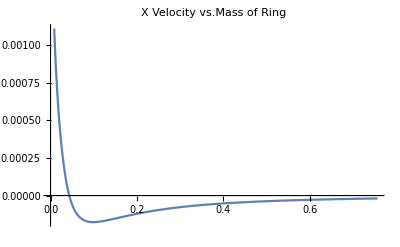

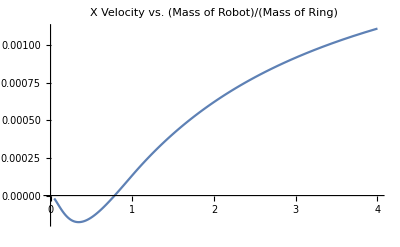

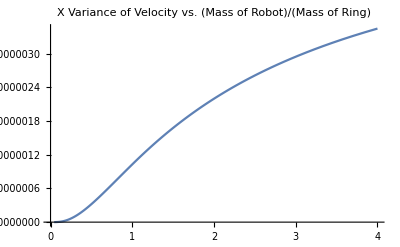

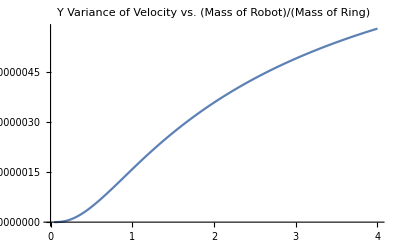

```mathematica
xx={};
xx2={};
xx3={};
xx4={};
xx5={};
i=0;
While[i<Length@Ai,
A0=.05;
ω=2 π 3;
T=120;
f=3.5;
λ1=.76;
λ2=1-λ1;
m=.034;
m1=(3m)/35;
m2=(28m)/34;
g=9.81;
μ=.37;
A=Ai[[i+1]];
B=Bi[[i+1]];
ϕ=π/5;
AppendTo[xx,{.25m+.01*i m,-f((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π}];
AppendTo[xx2,{1/(.25+i*.01),-f((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π}];
AppendTo[xx3,{1/(.25+i*.01),-f/(4 π^3 T)(-4 A B λ1 (1+2 λ1) (π+ϕ-λ1 ϕ)-B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ+6 (-1+λ1) λ1 ϕ)+A^2 (π^3 (-2+λ1)+π (2+4 λ1^2)+2 π^2 ϕ-2 (-1+λ1) (1+2 λ1^2) ϕ)-2 (A-B λ1) (π+ϕ-λ1 ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])+π^2 (A^2-B^2 λ1) Sin[2 ϕ])}];
AppendTo[xx4,{1/(.25+i*.01),f(B^2 λ1 (π+2 ϕ)-A^2 (π (-2+λ1)+2 ϕ)+(A^2-B^2 λ1) Sin[2 ϕ])/(4 π T)}];
AppendTo[xx5,{1/(.25+i*.01),(f(B^2 λ1 (π+2 ϕ)-A^2 (π (-2+λ1)+2 ϕ)+(A^2-B^2 λ1) Sin[2 ϕ])/(4 π T))/(-f/(4 π^3 T)(-4 A B λ1 (1+2 λ1) (π+ϕ-λ1 ϕ)-B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ+6 (-1+λ1) λ1 ϕ)+A^2 (π^3 (-2+λ1)+π (2+4 λ1^2)+2 π^2 ϕ-2 (-1+λ1) (1+2 λ1^2) ϕ)-2 (A-B λ1) (π+ϕ-λ1 ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])+π^2 (A^2-B^2 λ1) Sin[2 ϕ]))}];
i++;
];

ListLinePlot[xx,PlotRange->All,PlotLabel->"X Velocity vs.Mass of Ring"]
ListLinePlot[xx2,PlotRange->All,PlotLabel->"X Velocity vs. (Mass of Robot)/(Mass of Ring)"]
ListLinePlot[xx3,PlotRange->All,PlotLabel->"X Variance of Velocity vs. (Mass of Robot)/(Mass of Ring)"]
ListLinePlot[xx4,PlotRange->All,PlotLabel->"Y Variance of Velocity vs. (Mass of Robot)/(Mass of Ring)"]
```

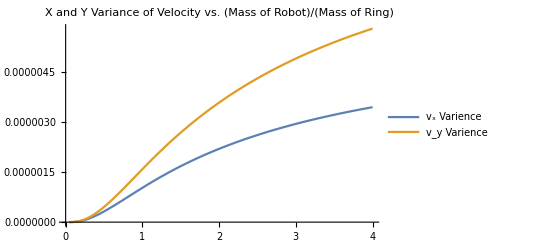

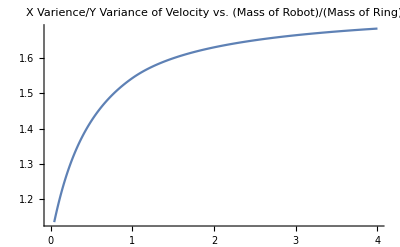

```mathematica
ListLinePlot[{xx3,xx4},PlotRange->All,PlotLabel->"X and Y Variance of Velocity vs. (Mass of Robot)/(Mass of Ring)",PlotLegends->{"v_x Varience","v_y Varience"}]
ListLinePlot[xx5,PlotRange->All,PlotLabel->"X Varience/Y Variance of Velocity vs. (Mass of Robot)/(Mass of Ring)"]
```

```mathematica
xx390=xx3;
```

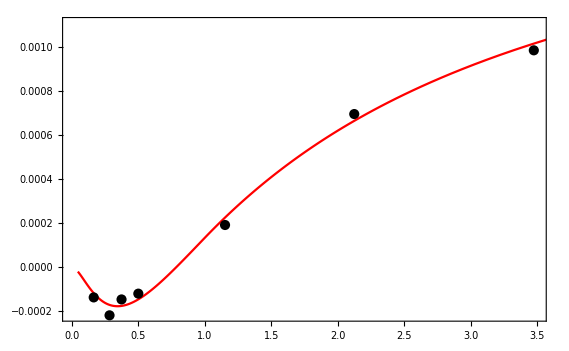

```mathematica
aa=ListLinePlot[xx2,PlotRange->All,PlotStyle->Red];
data={{0.164251208,-0.000136414},{0.283333333,-0.000217871},{0.373626374,-0.000145655},{.5,-0.00011935},{1.152542373,0.000192712},{2.125,0.000696996},{3.476482618,0.000986678}};
bb=ListPlot[data,Joined->False,Mesh->All,PlotStyle->Black];
Show[aa,bb,PlotRange->{{0,3.5},All},Frame->True]
```

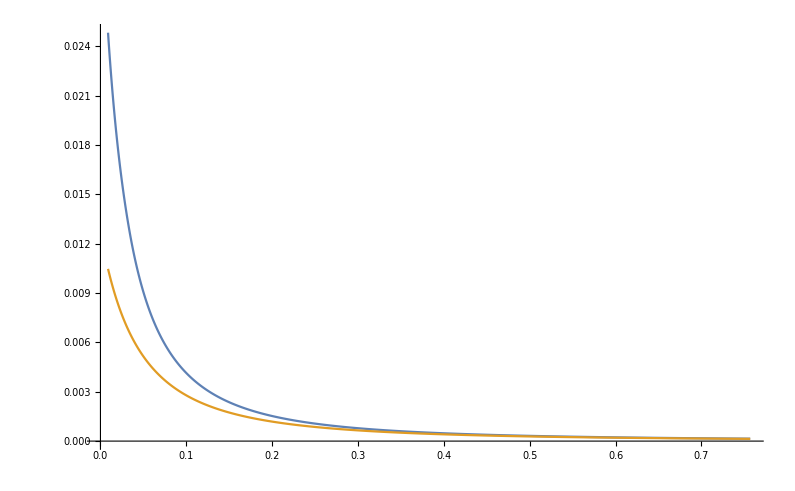

```mathematica
ListLinePlot[{Table[{.25m+.01*i m,Ai[[i]]},{i,1,Length@Ai}],Table[{.25m+.01*i m,Bi[[i]]},{i,1,Length@Ai}]},PlotRange->All(*{{0,.05},All}*)]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Clear[i]
```

```mathematica
datae={{{0.164251208,-0.000136414},ErrorBar[.000119176]},{{0.283333333,-0.000217871},ErrorBar[.000272568]},{{0.373626374,-0.000145655},ErrorBar[.000422338]},{{.5,-0.00011935},ErrorBar[.000655704]},{{1.152542373,0.000192712},ErrorBar[.00119943]},{{2.125,0.000696996},ErrorBar[.001004625]},{{3.476482618,0.000986678},ErrorBar[.001004625]}};
datae2={{{0.164251208,-0.000136414},ErrorBar[Sqrt[xx3120[[594,2]]]]},{{0.283333333,-0.000217871},ErrorBar[Sqrt[xx3150[[328,2]]]]},{{0.373626374,-0.000145655},ErrorBar[Sqrt[xx3120[[243,2]]]]},{{.5,-0.00011935},ErrorBar[Sqrt[xx3120[[175,2]]]]},{{1.152542373,0.000192712},ErrorBar[Sqrt[xx3120[[62,2]]]]},{{2.125,0.000696996},ErrorBar[Sqrt[xx3120[[22,2]]]]},{{3.476482618,0.000986678},ErrorBar[Sqrt[xx390[[4,2]]]]}};
```

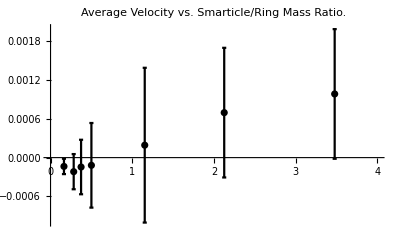

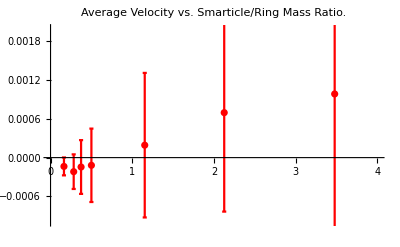

```mathematica
hw=.05;
bbb=ErrorListPlot[datae,PlotStyle->Black,PlotRange->{{0,4},{-.001,.002}},ErrorBarFunction->Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]},coords+{0,errs[[2,1]]}}],(*horizontal tick 1:*){Black,Thick,Line[{coords-{hw/2,-errs[[2,1]]},coords+{hw/2,errs[[2,1]]}}]},(*horizontal tick 2:*){Black,Thick,Line[{coords-{hw/2,errs[[2,1]]},coords+{hw/2,-errs[[2,1]]}}]}}],PlotRange->{{0,4},{-.001,.002}},PlotStyle->{Black},PlotLabel->"Average Velocity vs. Smarticle/Ring Mass Ratio."]
bb2=ErrorListPlot[datae2,ErrorBarFunction->Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]},coords+{0,errs[[2,1]]}}],(*horizontal tick 1:*){Red,Thick,Line[{coords-{hw/2,-errs[[2,1]]},coords+{hw/2,errs[[2,1]]}}]},(*horizontal tick 2:*){Red,Thick,Line[{coords-{hw/2,errs[[2,1]]},coords+{hw/2,-errs[[2,1]]}}]}}],PlotRange->{{0,4},{-.001,.002}},PlotStyle->{Red},PlotLabel->"Average Velocity vs. Smarticle/Ring Mass Ratio."]
```

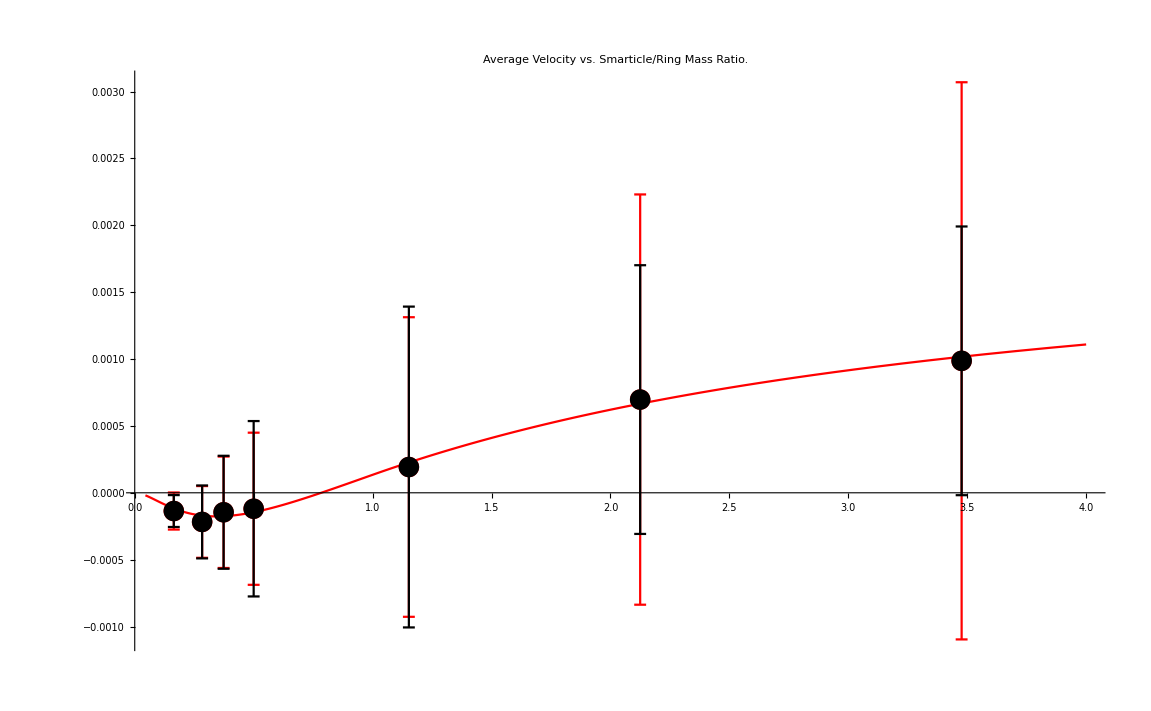

```mathematica
Show[bb2,aa,bbb,PlotRange->All]
```

Expectation X

```mathematica
Clear[A0,ω,m,m1,m2,g,μ,γ,mr,mb]
```

```mathematica
1/(2π) (λ1( Integrate[B Cos[θ],{θ,0 ,ϕ}]+ Integrate[A Cos[θ],{θ,ϕ ,π/2}]+ Integrate[B Cos[θ],{θ,π/2 ,3 π/2}]+Integrate[A Cos[θ],{θ,3 π/2 ,2π-ϕ}]+Integrate[B Cos[θ],{θ,2π-ϕ ,2π}])+λ2 Integrate[A Cos[θ],{θ,ϕ,2π-ϕ}])
```

(-2 A λ2 Sin[ϕ]+λ1 (2 A-2 B-2 A Sin[ϕ]+2 B Sin[ϕ]))/(2 π)

```mathematica
FullSimplify[%]
```

-((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/π

```mathematica
%/.λ2->(1-λ1)
```

-((-A+B) λ1+(A-B λ1) Sin[ϕ])/π

```mathematica
Clear[A,B,λ1,λ2,ϕ,T]
```

Varience X

```mathematica
1/(2π)(λ1( Integrate[((B Cos[θ])/T+((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/(T π))^2,{θ,0 ,ϕ}]+ Integrate[((A Cos[θ])/T+((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/(T π))^2,{θ,ϕ ,π/2}]+ Integrate[((B Cos[θ])/T+((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/(T π))^2,{θ,π/2 ,3 π/2}]+Integrate[((A Cos[θ])/T+((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/(T π))^2,{θ,3 π/2 ,2π-ϕ}]+Integrate[((B Cos[θ])/T+((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/(T π))^2,{θ,2π-ϕ ,2π}])+λ2 Integrate[((A Cos[θ])/T+((-A+B) λ1+(-B λ1+A (λ1+λ2)) Sin[ϕ])/(T π))^2,{θ,ϕ,2π-ϕ}])
```

1/(2 π)(-1/(π^2 T^2)λ2 (-A^2 π^3+2 A^2 π λ1-2 A B π λ1-3 A^2 π λ1^2+6 A B π λ1^2-3 B^2 π λ1^2+2 A^2 π λ2-2 A^2 π λ1 λ2+2 A B π λ1 λ2-A^2 π λ2^2+A^2 π^2 ϕ+3 A^2 λ1^2 ϕ-6 A B λ1^2 ϕ+3 B^2 λ1^2 ϕ+2 A^2 λ1 λ2 ϕ-2 A B λ1 λ2 ϕ+A^2 λ2^2 ϕ+(-B λ1+A (λ1+λ2)) (B λ1 (-π+ϕ)+A (π (-2+λ1+λ2)-(λ1+λ2) ϕ)) Cos[2 ϕ]+(4 (A-B) λ1 (B λ1 (-π+ϕ)+A (π (-1+λ1+λ2)-(λ1+λ2) ϕ))+A^2 π^2 Cos[ϕ]) Sin[ϕ])+λ1 (1/(2 π T^2)(B^2 π^2+8 A B λ1-8 B^2 λ1+3 A^2 λ1^2-6 A B λ1^2+3 B^2 λ1^2+2 A^2 λ1 λ2-2 A B λ1 λ2+A^2 λ2^2-(B λ1-A (λ1+λ2))^2 Cos[2 ϕ]-4 (-B (-2+λ1)+A λ1) (-B λ1+A (λ1+λ2)) Sin[ϕ])+1/(π^2 T^2)(2 A B π λ1-2 B^2 π λ1+2 A B π λ2+B^2 π^2 ϕ+3 A^2 λ1^2 ϕ-6 A B λ1^2 ϕ+3 B^2 λ1^2 ϕ+2 A^2 λ1 λ2 ϕ-2 A B λ1 λ2 ϕ+A^2 λ2^2 ϕ-(-B λ1+A (λ1+λ2)) (A (λ1+λ2) ϕ+B (2 π-λ1 ϕ)) Cos[2 ϕ]+(-4 (A-B) λ1 (A (λ1+λ2) ϕ+B (π-λ1 ϕ))+B^2 π^2 Cos[ϕ]) Sin[ϕ])-1/(2 π^2 T^2)(-A^2 π^3+12 A^2 π λ1-12 A B π λ1-3 A^2 π λ1^2+6 A B π λ1^2-3 B^2 π λ1^2+4 A^2 π λ2-2 A^2 π λ1 λ2+2 A B π λ1 λ2-A^2 π λ2^2+2 A^2 π^2 ϕ+6 A^2 λ1^2 ϕ-12 A B λ1^2 ϕ+6 B^2 λ1^2 ϕ+4 A^2 λ1 λ2 ϕ-4 A B λ1 λ2 ϕ+2 A^2 λ2^2 ϕ+(-B λ1+A (λ1+λ2)) (-B λ1 (π-2 ϕ)+A (π (-4+λ1+λ2)-2 (λ1+λ2) ϕ)) Cos[2 ϕ]+4 (B^2 λ1^2 (π-2 ϕ)+A^2 (π (λ1^2+λ1 (-4+λ2)-2 λ2)-2 λ1 (λ1+λ2) ϕ)+A B λ1 (-π (-4+2 λ1+λ2)+2 (2 λ1+λ2) ϕ)) Sin[ϕ]+A^2 π^2 Sin[2 ϕ])))

```mathematica
FullSimplify[%]
```

1/(4 π^3 T^2)(-4 A B λ1 (3 λ1+λ2) (π (-2+λ1+λ2)-λ2 ϕ)+B^2 λ1 (π^3+6 π λ1 (-2+λ1+λ2)+2 π^2 ϕ-6 λ1 λ2 ϕ)+A^2 (π^3 (λ1+2 λ2)+2 π (-2+λ1+λ2) (3 λ1^2+2 λ1 λ2+λ2^2)-2 π^2 (λ1+λ2) ϕ-2 λ2 (3 λ1^2+2 λ1 λ2+λ2^2) ϕ)-2 (-B λ1+A (λ1+λ2)) (π (-2+λ1+λ2)-λ2 ϕ) ((-B λ1+A (λ1+λ2)) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])-π^2 (-B^2 λ1+A^2 (λ1+λ2)) Sin[2 ϕ])

```mathematica
%/.λ2->(1-λ1)
```

1/(4 π^3 T^2)(-4 A B λ1 (1+2 λ1) (-π-(1-λ1) ϕ)+B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ-6 (1-λ1) λ1 ϕ)+A^2 (π^3 (2 (1-λ1)+λ1)-2 π ((1-λ1)^2+2 (1-λ1) λ1+3 λ1^2)-2 π^2 ϕ-2 (1-λ1) ((1-λ1)^2+2 (1-λ1) λ1+3 λ1^2) ϕ)-2 (A-B λ1) (-π-(1-λ1) ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])-π^2 (A^2-B^2 λ1) Sin[2 ϕ])

```mathematica
FullSimplify[%]
```

-1/(4 π^3 T^2)(-4 A B λ1 (1+2 λ1) (π+ϕ-λ1 ϕ)-B^2 λ1 (π^3-6 π λ1+2 π^2 ϕ+6 (-1+λ1) λ1 ϕ)+A^2 (π^3 (-2+λ1)+π (2+4 λ1^2)+2 π^2 ϕ-2 (-1+λ1) (1+2 λ1^2) ϕ)-2 (A-B λ1) (π+ϕ-λ1 ϕ) ((A-B λ1) Cos[2 ϕ]+4 (A-B) λ1 Sin[ϕ])+π^2 (A^2-B^2 λ1) Sin[2 ϕ])

Expectation Y

```mathematica
1/(2π) (λ1( Integrate[B Sin[θ],{θ,0 ,ϕ}]+ Integrate[A Sin[θ],{θ,ϕ ,π/2}]+ Integrate[B Sin[θ],{θ,π/2 ,3 π/2}]+Integrate[A Sin[θ],{θ,3 π/2 ,2π-ϕ}]+Integrate[B Sin[θ],{θ,2π-ϕ ,2π}])+λ2 Integrate[A Sin[θ],{θ,ϕ,2π-ϕ}])
```

(λ1 (B+B (-1+Cos[ϕ])-B Cos[ϕ]))/(2 π)

```mathematica
FullSimplify[%]
```

0

Varience Y

```mathematica
1/(2π)(λ1( Integrate[((B Sin[θ])/T)^2,{θ,0 ,ϕ}]+ Integrate[((A Sin[θ])/T)^2,{θ,ϕ ,π/2}]+ Integrate[((B Sin[θ])/T)^2,{θ,π/2 ,3 π/2}]+Integrate[((A Sin[θ])/T)^2,{θ,3 π/2 ,2π-ϕ}]+Integrate[((B Sin[θ])/T)^2,{θ,2π-ϕ ,2π}])+λ2 Integrate[((A Sin[θ])/T)^2,{θ,ϕ,2π-ϕ}])
```

((A^2 λ2 (π-ϕ+Cos[ϕ] Sin[ϕ]))/T^2+λ1 ((B^2 π)/(2 T^2)+(B^2 (ϕ-Cos[ϕ] Sin[ϕ]))/T^2+(A^2 (π-2 ϕ+Sin[2 ϕ]))/(2 T^2)))/(2 π)

```mathematica
FullSimplify[%]
```

1/(4 π T^2)(B^2 λ1 (π+2 ϕ)+A^2 (π (λ1+2 λ2)-2 (λ1+λ2) ϕ)+(-B^2 λ1+A^2 (λ1+λ2)) Sin[2 ϕ])

```mathematica
%/.λ2->(1-λ1)
```

(A^2 (π (2 (1-λ1)+λ1)-2 ϕ)+B^2 λ1 (π+2 ϕ)+(A^2-B^2 λ1) Sin[2 ϕ])/(4 π T^2)

```mathematica
FullSimplify[%]
```

(B^2 λ1 (π+2 ϕ)-A^2 (π (-2+λ1)+2 ϕ)+(A^2-B^2 λ1) Sin[2 ϕ])/(4 π T^2)

Histogram Stuff

```mathematica
ϕ=π/5;
ψ={};
A=Ai[[22]];
B=Bi[[22]];
tot=0;
T=120;
n=T*3.5;
nn=10000;
j=1;
While[j<nn,
tot=0;
i=1;
While[i<n+1,
ζ=RandomReal[{0,2π}];
ξ=RandomReal[{0,1}];

If[ξ≤.76,

If[ζ<ϕ,
η=B Cos[ζ];
];
If[ζ<π/2&&ζ>ϕ,
η=A Cos[ζ];
];
If[ζ>π/2&&ζ<3 π/2,
η=B Cos[ζ];
];
If[ζ>(3π)/2&&ζ<2π-ϕ,
η=A Cos[ζ];
];
If[ζ>2π-ϕ,
η=B Cos[ζ];
];
];

If[ξ>.76,

If[ζ<ϕ,
η=0;
];
If[ζ<π/2&&ζ>ϕ,
η=A Cos[ζ];
];
If[ζ>π/2&&ζ<3 π/2,
η=A Cos[ζ];
];
If[ζ>(3π)/2&&ζ<2π-ϕ,
η=A Cos[ζ];
];
If[ζ>2π-ϕ,
η=0;
];
];

tot=tot+η;
i++;
];
AppendTo[ψ,tot/T];
j++;
];
```

```mathematica
aaa1=Histogram[ψ,50,"PDF"];
```

```mathematica
aaa2=Plot[PDF[NormalDistribution[xx2[[22,2]],Sqrt[xx3[[22,2]]]],x],{x,-.005,.005}];
```

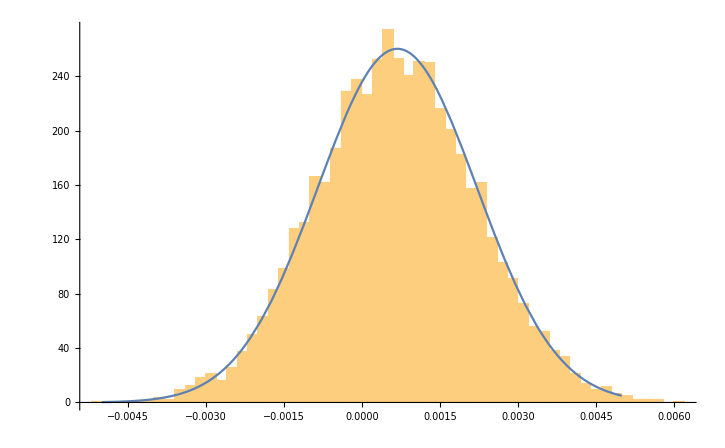

```mathematica
Show[aaa1,aaa2]
```

```mathematica
xx2
```

{{4.,0.00108391},{3.84615,-0.314324}}

```mathematica
xx2
```

{{4.,0.0011091},{3.84615,0.00108391},{3.7037,0.00105931},{3.57143,0.00103527},2194,{0.0449843,-0.0000191946},{0.044964,-0.0000191801},{0.0449438,-0.0000191655}}
 |  |  |  |

```mathematica
Length[xx2]
```

2201